```mathematica
Sin[x]^2+Cos[x]^2
```

Cos[x]^2+Sin[x]^2

```mathematica
Simplify[%]
```

1

```mathematica
2*((Sin[x])^2 + (Cos[x])^2)
Simplify[%]
```

2 (Cos[x]^2+Sin[x]^2)

2

```mathematica
2 (Cos[x]^2+Sin[x]^2)

200!
```

2 (Cos[x]^2+Sin[x]^2)

788657867364790503552363213932185062295135977687173263294742533244359449963403342920304284011984623904177212138919638830257642790242637105061926624952829931113462857270763317237396988943922445621451664240254033291864131227428294853277524242407573903240321257405579568660226031904170324062351700858796178922222789623703897374720000000000000000000000000000000000000000000000000

```mathematica
2^(2^(2^2))
```

65536

```mathematica
2^2^2^2!
```

65536

```mathematica
D[x^n,x]
```

n x^(-1+n)

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
"Свой пример 4"
```

```mathematica
Integrate[Sin[x], x]
```

-Cos[x]

```mathematica
Integrate[Cos[x], x]
```

```mathematica
Sin[x]
"end;"
```

```mathematica
Simplify[Integrate[sin[x], x]]
```

∫sin[x]ⅆx

```mathematica
FactorInteger[123456789123456789]
```

{{3,2},{7,1},{11,1},{13,1},{19,1},{3607,1},{3803,1},{52579,1}}

```mathematica
Solve[a*x^2+b*x+c==0,x]
```

```mathematica
{{x->(-b-√(b^2-4 a c))/(2 a)},{x->(-b+√(b^2-4 a c))/(2 a)}}
"Свой пример 1"
Solve[x^2-1==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
{{x->-1},{x->1}}
"end;"
```

```mathematica
Solve[a*x^3+b*x^2+c*x+d==0,x]
```

{{x→-b/(3 a)-(2^(1/3) (-b^2+3 a c))/(3 a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))+((-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(3 2^(1/3) a)},{x→-b/(3 a)+((1+ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-1/(6 2^(1/3) a)(1-ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3)},{x→-b/(3 a)+((1-ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-1/(6 2^(1/3) a)(1+ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3)}}

```mathematica
Solve[a*x^10+x^2==0,x]
```

{{x→0},{x→0},{x→-(-1)^(1/8)/a^(1/8)},{x→(-1)^(1/8)/a^(1/8)},{x→-(-1)^(3/8)/a^(1/8)},{x→(-1)^(3/8)/a^(1/8)},{x→-(-1)^(5/8)/a^(1/8)},{x→(-1)^(5/8)/a^(1/8)},{x→-(-1)^(7/8)/a^(1/8)},{x→(-1)^(7/8)/a^(1/8)}}

```mathematica
Series[Sin[x],{x,1,5}]
```

Sin[1]+Cos[1] (x-1)-1/2 Sin[1] (x-1)^2-1/6 Cos[1] (x-1)^3+1/24 Sin[1] (x-1)^4+1/120 Cos[1] (x-1)^5+O[x-1]^6

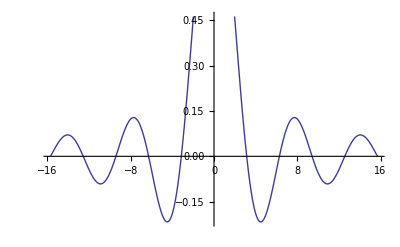

```mathematica
Plot[Sin[x]/x,{x,-5Pi,5Pi}]
```

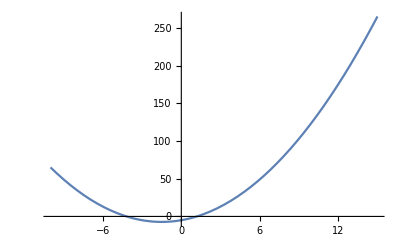

```mathematica
Plot[x^2+3*x-5,{x,-10,15}]
```

```mathematica
"Свой пример 2"
Plot[E^x, {x,0, 20}]
```

Свой пример 2

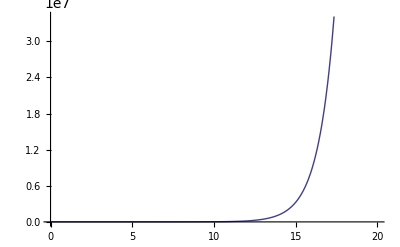

```mathematica
"end;"
```

```mathematica
z=Sin[x*y]
Plot3D[z,{x,-2,2},{y,-4,3}]
```

```mathematica
Sin[x y]
```

-Graphics3D-

```mathematica
"Свой пример 3"
z = Tan[x/y]
Plot3D[z,{x, -10Pi, 10Pi}, {y, -10Pi, 10Pi}]
```

Tan[x/y]

-Graphics3D-

```mathematica
z = (x^2 + y^2)
Plot3D[z, {x, -1000, +1000},{y, -2000, 2000}]
```

x^2+y^2

-Graphics3D-

```mathematica
"end;"
```